```mathematica
SetDirectory[NotebookDirectory[]];
<<RLBotIO`
<<RLBotMisc`
```

```mathematica
AirTorque = {-400.0, -130.0, 95.0};
AirDamping  = {-50.0, -30.0, -20.0};
ωMaxAerial= 5.5;
αMax = 9.0;
J =10.5;
Δt= 1/60.0;

scale = DiagonalMatrix[{1/ωMaxAerial,1/ωMaxAerial,1/ωMaxAerial,1/π,1/π,1/π}];
```

```mathematica
rollParameters = {T ->400.0/10.5, b -> 50.0/10.5};
GRoll[ω_] :=(RealSign[ω] (b RealAbs[ω]+T Log[T/(T+b RealAbs[ω])])/b^2 + 0.00 ω)/. rollParameters
DGRoll[ω_] := (FullSimplify[D[GRoll[zz], zz], Assumptions->zz≠ 0] /. zz->ω )/. rollParameters;
pitchParameters = {T ->130.0/10.5};
GPitch[ω_] :=( 1/2((RealSign[ω] ω^2)/T)+ 0.00ω)/.pitchParameters
DGPitch[ω_] := (FullSimplify[D[GPitch[zz], zz], Assumptions->zz≠ 0] /. zz->ω )/.pitchParameters;
yawParameters = {T ->95.0/10.5};
GYaw[ω_] :=( 1/2((RealSign[ω] ω^2)/T)+ 0.00 ω)/.yawParameters
DGYaw[ω_] := (FullSimplify[D[GYaw[zz], zz], Assumptions->zz≠ 0] /. zz->ω )/.yawParameters;

G[ω_] := {GRoll[ω[[1]]], GPitch[ω[[2]]], GYaw[ω[[3]]]}
dG[ω_] := {DGRoll[ω[[1]]], DGPitch[ω[[2]]], DGYaw[ω[[3]]]}


Z[θ_] := Module[{Ω0=Ω[θ]},IdentityMatrix[3] + Sum[BernoulliB[i]/(i!) MatrixPower[Ω0, i], {i, 1, 2}]]
r[s_, α_, Δt_] := Module[{ω, ϕ, θ, ωpred, ϕpred, ϕdot},
ω = s[[1;;3]];
ϕ = s[[4;;6]];
θ = AxisAngleRotation[ϕ];
ωpred = ω + θ.α Δt;
ϕpred = ϕ + Z[ϕ].(ω+1/2 θ.α Δt) Δt;
ϕdot = Z[ϕpred].ωpred;
-ϕpred - G[ϕdot]
]

GetControlForAcceleration[α_, values_] := Module[{αclipped = Clip[α, {Min[values], Max[values]}]},
If[Min[values[[1;;2]]] ≤ αclipped ≤Max[values[[1;;2]]],
If[Abs[values[[2]]-values[[1]]] < 10^-4, -0.5, (αclipped- values[[2]])/(values[[2]]-values[[1]]) ],
If[Abs[values[[3]]-values[[2]]] < 10^-4, 0.5, (αclipped- values[[2]])/(values[[3]]-values[[2]]) ]
]
]

NewController[s_] := Module[{ω,ωLocal,ϕ,ϕdot,θ,α,idealα,possibleα, r0, drdα},
ω = s[[1;;3]];
ϕ = s[[4;;6]];
θ = AxisAngleRotation[ϕ];
ωLocal = Transpose[θ].ω;
ϕdot = Z[ϕ].ω;
possibleα =1/J({{-T1+D1 ωLocal[[1]], D1 ωLocal[[1]], T1+D1 ωLocal[[1]]}, {-T2, D2 ωLocal[[2]], T2}, {-T3, D3 ωLocal[[3]], T3}})/. torques;
idealα = {0.0, 0.0, 0.0};
ϵ = 0.001;
Do[
r0=r[s, idealα, 2Δt];
drdα=1/ϵ Transpose[{
r0-r[s, idealα+{ϵ,0,0}, 2Δt],
r0-r[s, idealα+{0,ϵ,0}, 2Δt],
r0-r[s, idealα+{0,0,ϵ}, 2Δt]
}];
idealα += LinearSolve[drdα, r0];
,
{i, 1, 5}
];
Table[GetControlForAcceleration[idealα[[i]], possibleα[[i]]], {i, 1, 3}]
]
```

```mathematica
Clear[Z]
```

```mathematica
θ = RandomReal[{-3, 3}, 3]
```

{-2.94934,-0.740805,-2.66413}

```mathematica
Z[θ]
```

{{0.3628,-1.14999,1.02519},{1.51414,-0.316351,-1.3102},{0.284384,1.63914,0.229383}}

```mathematica
Y[θ]
```

{{0.0746219,-1.06765,1.32132},{1.59648,-0.91168,-1.23582},{0.580516,1.71352,-0.119133}}

```mathematica
getRPY[ω0_, ωT_, J_, θ_, Δt_] := Module[{
Ω0 = Transpose[θ].ω0, 
ΩT= Transpose[θ].ωT,
T = AirTorque,
H = AirDamping,
a,b,c
},
a = Table[Δt/J T[[i]], {i, 1, 3}];
b = Table[ -Δt/J H[[i]] Ω0[[i]], {i, 1, 3}];b[[1]] = 0;
c = Table[ΩT[[i]]-(1 + Δt/J H[[i]])Ω0[[i]], {i, 1, 3}];
Table[solvePWL[a[[i]], b[[i]], c[[i]]], {i, 1, 3}]
]

q[x_]:= 1-1/(1+500 x^2)
res[Δx_, v_]:=Δx-Sign[v] 1/2 v^2/αMax
controller[Δx_, v_, Δt_] := Module[{ri,a, rf},
ri=res[Δx, v];
a = Sign[ri]αMax ;
rf = res[Δx-v Δt,v+a Δt];
If[ri * rf < 0,a(2 ri/(ri-rf)-1),a]
]

OldController[s_] := Module[{ω, θ,α,Δθ, ϕLocal, ϕWorld, error},
ω = s[[1;;3]];
θ = AxisAngleRotation[s[[4;;6]]];
Δθ=Transpose[θ];
ϕLocal=RotationAxis[Δθ];
ϕWorld=θ.ϕLocal;

error = Abs[ϕWorld] + Abs[ω];

α =  Table[q[error[[i]]]controller[ϕWorld[[i]],ω[[i]], Δt],{i,1,3}];
getRPY[ω, ω + α Δt, J, θ, Δt] 
]
```

```mathematica
Accelerations[{u1_, u2_, u3_}] := Module[{T, H},
T = DiagonalMatrix[{T1, T2, T3}];
H = DiagonalMatrix[{D1, D2, D3} * {1,(1-Abs[u2]), (1-Abs[u3])}];
T.{u1, u2, u3}+H.{ω1, ω2, ω3}
]

torques = Thread[{T1, T2, T3, D1, D2, D3} -> Join[AirTorque, AirDamping]];
{
Chop[Accelerations[{#, 0, 0}][[1]]]& /@ {-1, 0, 1},
Chop[Accelerations[{0, #, 0}][[2]]]& /@ {-1, 0, 1},
Chop[Accelerations[{0, 0, #}][[3]]]& /@ {-1, 0, 1}
}

{{-T1+D1 ω1,D1 ω1,T1+D1 ω1},{-T2,D2 ω2,T2},{-T3,D3 ω3,T3}} /. torques
```

{{-T1+D1 ω1,D1 ω1,T1+D1 ω1},{-T2,D2 ω2,T2},{-T3,D3 ω3,T3}}

{{400.-50. ω1,-50. ω1,-400.-50. ω1},{130.,-30. ω2,-130.},{-95.,-20. ω3,95.}}

```mathematica
nextState[s_, a_] := Module[
{T, H, τ, ω, θ},
ω = s[[1;;3]];
θ = AxisAngleRotation[s[[4;;6]]];
T = DiagonalMatrix[AirTorque];
H = DiagonalMatrix[AirDamping * {1,(1-Abs[a[[2]]]), (1-Abs[a[[3]]])}];
τ = θ.(T.a+H.Transpose[θ].ω);
ω = ω + τ/J Δt ;
ω *= Min[1.0, ωMaxAerial/Norm[ω]];
θ = RotationAxis[AxisAngleRotation[ω Δt].θ];
If[θ.s[[4;;6]]<-3.0, θ -= 2π Normalize[θ]];
Join[ω, θ]
]

RandomState[] := Module[{s = RandomReal[{-1, 1}, 6] * {ωMaxAerial, ωMaxAerial, ωMaxAerial, 4, 4, 4}},
While[Norm[s[[1;;3]]] > ωMaxAerial,
s = RandomReal[{-1, 1}, 6] * {ωMaxAerial, ωMaxAerial, ωMaxAerial, 4, 4, 4}
];
s
]

SimulateTrajectory[s0_, controlFunc_] := Module[{s,a,t, times, states, actions, rewards, count},
t = 0.0;
s = s0;

times = {};
states = {};
actions = {};

Do[
a = controlFunc[s];
s = nextState[s, a];
t += Δt;
AppendTo[times,t];
AppendTo[states,s];
AppendTo[actions,a];
If[Norm[s[[1;;3]]]<0.01 && Norm[s[[4;;6]]]<0.01, Break[]]
,
{i,1,240}
];
{Reverse[times], states, actions}
]
```

```mathematica
s = s0
```

{0,-2.,0.,0.,-2.5,0}

```mathematica
αmax = 130/10.5
```

12.381

```mathematica
αmax
```

12.381

```mathematica
αmax = {-300.0, 130.0, 95.0}/10.5
```

{-28.5714,12.381,9.04762}

```mathematica
timeEstimate[s_] := Module[{ω, ϕ, ϕdot, Δϕ, t1, t2},

ω = s[[1;;3]];
ϕ = s[[4;;6]];
ϕdot = Z[ϕ].ω;
Δϕ = -ϕ- G[ϕdot];

t1 =-ϕdot/αmax;
t2 =2 Sqrt[Abs[Δϕ]/Abs[αmax]];
t1 + t2
]
```

{0.25095,0.,0.}

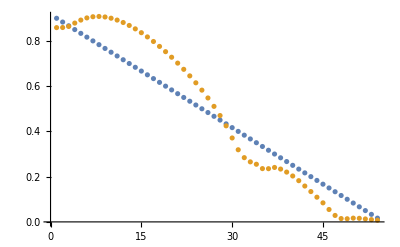

{1.2,{0.450056,0.669287,1.34182},1.18333,{0.495916,0.704375,1.22657},1.16667,135,0.0333333,{0.000171783,0.000674801,0.0123234},0.0166667,{0.000121561,0.000475793,0.00845196}}
 |  |  |  |

```mathematica
ListPlot[{
tNew,
Norm[timeEstimate[#]]& /@ statesNew
}]
```

```mathematica
s = RandomState[] * {1,1,1,1,1,1}
```

{-3.23809,-1.13975,2.99495,-2.61288,-0.890032,0.804132}

```mathematica
timeEstimate[s]
```

{0.476404,0.252912,0.764944}

```mathematica
timeEstimate[s - 2π Join[{0, 0, 0}, Normalize[s[[4;;6]]]]]
```

{0.671869,0.35668,1.0788}

```mathematica
Norm[timeEstimate[s]]
Norm[timeEstimate[s - 2π Join[{0, 0, 0}, Normalize[s[[4;;6]]]]]]
```

1.22792

0.860502

```mathematica
s[[4;;6]]-=2π Normalize[s[[4;;6]]]
```

{3.09735,1.05506,-0.95323}

{0.461986,0.474311,0.549601}

0.9

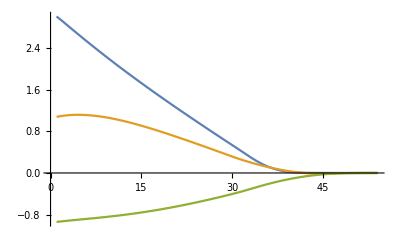
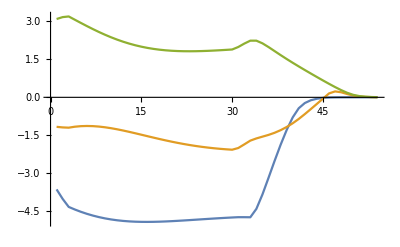
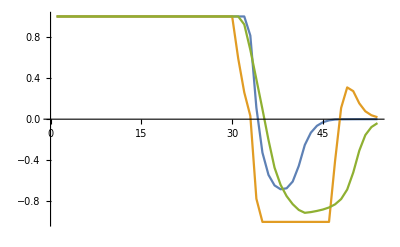

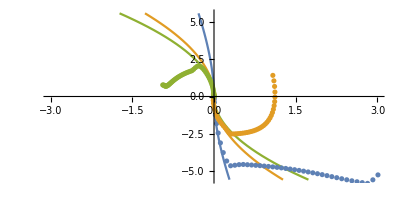

```mathematica
timeEstimate[s]
{tNew,statesNew, actionsNew}=SimulateTrajectory[s, NewController];
tNew[[1]]
PlotTrajectory[statesNew, actionsNew]
PlotStateSpace[statesNew]
```

```mathematica
θ = RandomReal[{-1, 1}, 3]4
```

{-3.92496,1.65989,1.1694}

```mathematica
Z[θ]
Y[θ]
```

{{0.656438,0.0417831,-1.21244},{-1.12762,-0.397737,-1.80072},{0.447458,2.12424,-0.513382}}

{{0.442488,-0.296312,-1.45063},{-1.46572,-1.26816,-1.69999},{0.209268,2.22497,-1.45582}}

```mathematica
Z[θ_] := Module[{Ω0=Ω[θ]},IdentityMatrix[3] + Sum[BernoulliB[i]/(i!) MatrixPower[Ω0, i], {i, 1, 2}]]
```

```mathematica
Z[θ_] := Module[{
A1 = Outer[Times, θ, θ]/(θ.θ),
A2 = -1/2({{0, -θ[[3]], θ[[2]]}, {θ[[3]], 0, -θ[[1]]}, {-θ[[2]], θ[[1]], 0}}),
A3 = 1/2(IdentityMatrix[3] -  Outer[Times, θ, θ]/(θ.θ))Cot[1/2 Norm[θ]]Norm[θ]
},
A1 + A2 + A3
]
```

```mathematica
s0 = RandomState[]
```

{3.44496,3.87922,-0.363913,3.60676,3.21316,3.86109}

```mathematica
s0 = {0,1.0, 0.0, 0.0, -0.3, 0}
```

{0,1.,0.,0.,-0.3,0}

```mathematica
s0 = RandomState[]
```

{-1.4136,4.2201,0.681369,-2.98061,-3.65151,-3.88944}

```mathematica
s0[[4;;6]]-=2π Normalize[s0[[4;;6]]]
```

{-2.98061,-3.65151,-3.88944}

```mathematica
s0
```

{-1.4136,4.2201,0.681369,0.0839417,0.102836,0.109537}

```mathematica
tNew
```

{1.,0.991667,0.983333,0.975,0.966667,0.958333,0.95,0.941667,0.933333,0.925,100,0.0833333,0.075,0.0666667,0.0583333,0.05,0.0416667,0.0333333,0.025,0.0166667,0.00833333}
 |  |  |  |

1.03333

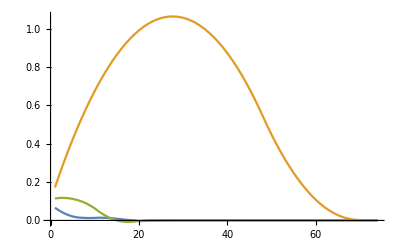
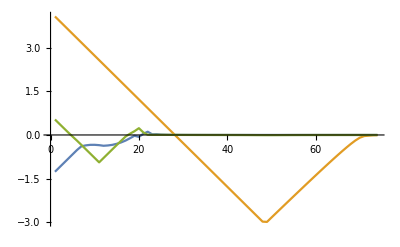
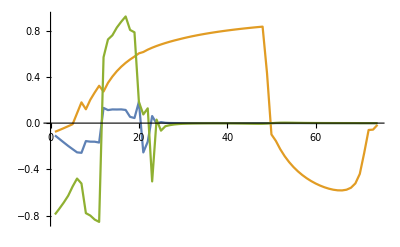

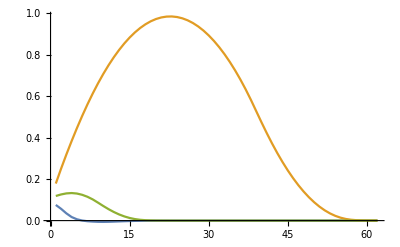
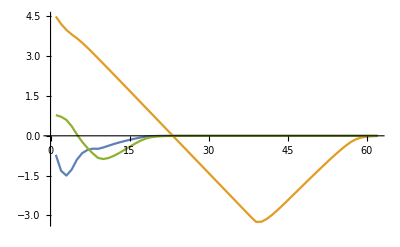
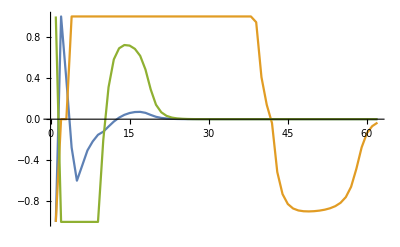

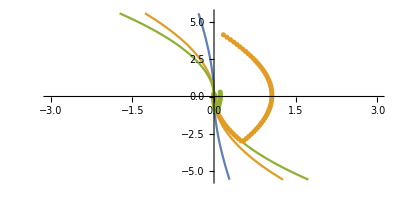

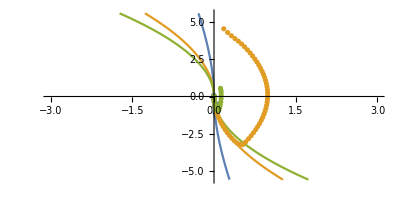

```mathematica
{tOld,statesOld, actionsOld}=SimulateTrajectory[s0, OldController];
{tNew,statesNew, actionsNew}=SimulateTrajectory[s0, NewController];
tNew[[1]]
PlotTrajectory[statesOld, actionsOld]
PlotTrajectory[statesNew, actionsNew]
PlotStateSpace[statesOld]
PlotStateSpace[statesNew]
```

```mathematica
PlotTrajectory[states_, actions_] := {
ListLinePlot[Transpose[states[[All,4;;6]]], PlotRange->All],
ListLinePlot[Transpose[states[[All,1;;3]]], PlotRange->All],
ListLinePlot[Transpose[actions], PlotRange->All]
}

PlotStateSpace[states_] := Module[{ϕdot = Z[#[[4;;6]]].#[[1;;3]]& /@ states},
Show[
ParametricPlot[{
{-G[{ω, ω, ω}][[1]],ω},
{-G[{ω, ω, ω}][[2]],ω},
{-G[{ω, ω, ω}][[3]],ω}
}, {ω,-5.6, 5.6}, Axes->True
],
ListPlot[{
Transpose[{states[[All, 4]],ϕdot[[All,1]]}],
Transpose[{states[[All, 5]],ϕdot[[All,2]]}],
Transpose[{states[[All, 6]],ϕdot[[All,3]]}]
}, PlotRange->All],
 PlotRange->{{-3,3},{-5.6, 5.6}},
AspectRatio->0.5
]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<RLBotMisc`
```

{0.050511,-2.1276,1.08439,1.70324,-0.511153,0.343538}

{-0.60775,-1.76577,1.07682,1.69306,-0.504337,0.340415}

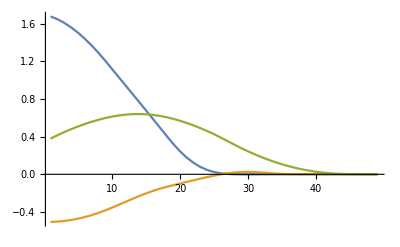
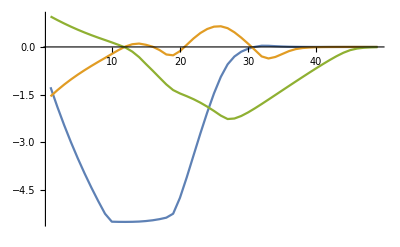
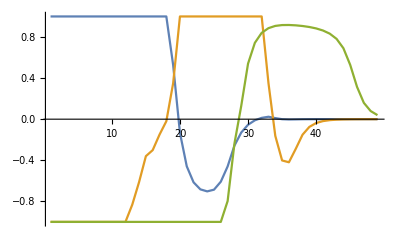

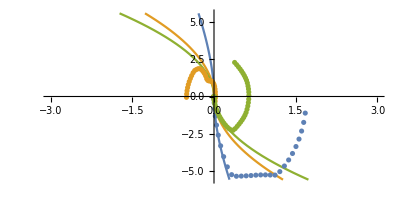

```mathematica
s = Flatten[{
data[[1,2;;4]],
RotationAxis[Partition[data[[1,5;;13]], 3]]
}]
{tNew,statesNew, actionsNew}=SimulateTrajectory[s, NewController];
PlotTrajectory[statesNew, actionsNew]
PlotStateSpace[statesNew]
```

```mathematica
data = Import["aerial_turn_simulation.csv"];
```

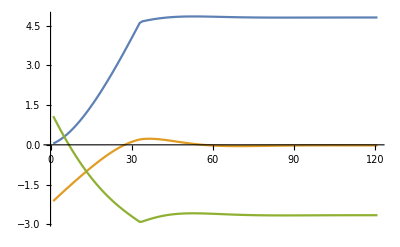

```mathematica
ListLinePlot[Transpose[history[[All,1;;3]]], PlotRange->All]
```

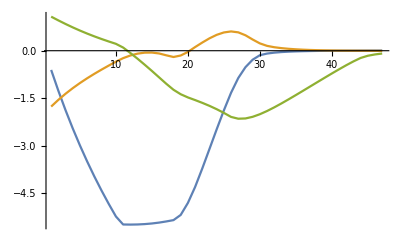

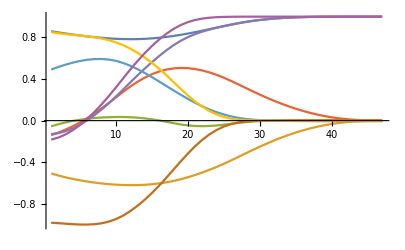

```mathematica
ListLinePlot[Transpose[data[[All, 2;;4]]], PlotRange->All]
ListLinePlot[Transpose[data[[All, 5;;13]]], PlotRange->All]
```